```mathematica
Quit
```

# Plots from lists

```mathematica
lista1={{1,2},{2,3},{3,4}};
```

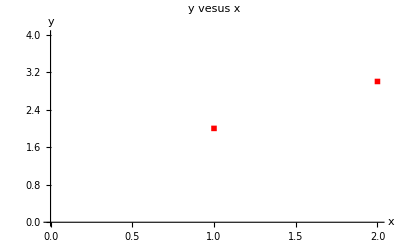

```mathematica
plot1=ListPlot[lista1,AxesLabel->{"x","y"},PlotLabel->"y vesus x",PlotStyle->Red,PlotMarkers->■,PlotRange->{{0,2},{0,4}}]
```

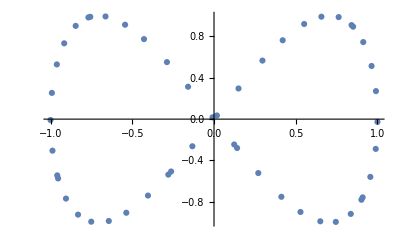

```mathematica
plot2=ListPlot[Table[{Sin[n],Sin[2n]},{n,50}]]
```

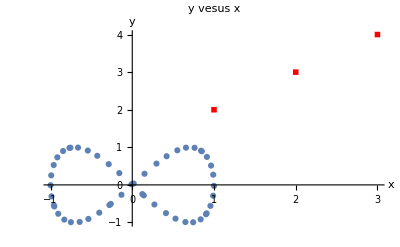

```mathematica
Show[plot1,plot2,PlotRange->All]
```